# Simulating Data

This code allows you to generate data from a Lagrangian give the boundary conditions at 2 locations within the data.

```mathematica
Needs["VariationalMethods`"]
```

```mathematica
SetDirectory["C:/Users/User/Goliath/resources"];
```

## SHO oscillator

```mathematica
L[th1_, w1_]:= w1^2 - th1^2;
```

Generate the Euler Equations

```mathematica
sol=EulerEquations[L[th1[t],  D[th1[t],t]], th1[t], t]
```

-2 (th1[t]+th1''[t])==0

```mathematica
sol1=NDSolve[{sol, th1[0]==1, th1[1]==1}, th1[t], {t,0,10.0}]
```

{{th1[t]→InterpolatingFunction[{{0., 10.}}, <>][t]}}

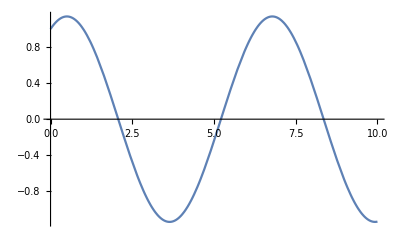

```mathematica
Plot[Evaluate[th1[t]/.sol1], {t, 0,10.0}, PlotRange->All]
```

```mathematica
deltat = 0.1
```

0.1

```mathematica
times = Range[0,10, deltat];
```

```mathematica
expth1 = Flatten[(th1[t]/.sol1)/.t->times];
```

```mathematica
results=Transpose[{expth1}];
```

```mathematica
Export["sho_0.1.csv", results, "CSV"];
```

## Coupled SHO

```mathematica
L1[th1_, th2_,  w1_, w2_]:= w1^2 + w2^2 - 2 th1^2 -  th2^2 + 2 th1 th2;
```

Generate the Euler Equations

```mathematica
sol2=EulerEquations[L1[th1[t], th2[t],  D[th1[t],t], D[th2[t],t] ], {th1[t], th2[t]}, t]
```

{-2 (2 th1[t]-th2[t]+th1''[t])==0,2 (th1[t]-th2[t]-th2''[t])==0}

```mathematica
sol3=NDSolve[{sol2, th1[0]==1, th1[1]==1, th2[0]== 2, th2[1]== 1}, {th1[t], th2[t]}, {t,0,10.0}]
```

{{th1[t]→InterpolatingFunction[{{0., 10.}}, <>][t],th2[t]→InterpolatingFunction[{{0., 10.}}, <>][t]}}

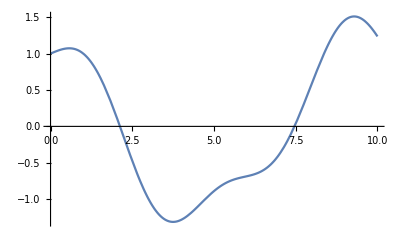

```mathematica
Plot[Evaluate[th1[t]/.sol3], {t, 0,10.0}, PlotRange->All]
```

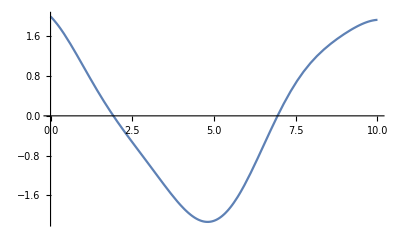

```mathematica
Plot[Evaluate[th2[t]/.sol3], {t,0,10.0}, PlotRange->All]
```

```mathematica
deltat1 = 0.1
```

0.1

```mathematica
times1= Range[0,10, deltat1];
```

```mathematica
expth11 = Flatten[(th1[t]/.sol3)/.t->times1];
```

```mathematica
expth12 = Flatten[(th2[t]/.sol3)/.t->times1];
```

```mathematica
results1=Transpose[{expth11, expth12}];
```

```mathematica
Export["sho_coupled_0.1.csv", results1, "CSV"];
```

## Pendulum attached to a mass on a spring

Mass M moves horizontally while attached to a spring of spring constant k. Hanging from the mass is a pendulum of arm length L and bob mass m
 				http://physics.ucsd.edu/students/courses/winter2008/physics110b/LECTURES/CH06_LAGRANGE.pdf

The data generated in this worksheet uses the ‘perfect’ solution to EL to find out w1, w2 etc and save them off to a data file. This way the errors associated with a discrete differential are avoided.

L2[th_, x_, w1_, xprime_] :=  0.5*(m + m2)*xprime^2 + 0.5*m2*(l^2)*w1^2 + m2*l*Cos[th]*xprime*w1 - 0.5*k*x^2 + m2*9.81*l*Cos[th]

m1 =  1
k =  1
l =  1
m2 = 1

```mathematica
L2[th_, x_, w1_, xprime_] :=  0.5*(1 + 1)*xprime^2 + 0.5*1*(1^2)*w1^2 + 1*1*Cos[th]*xprime*w1 - 0.5*1*x^2 + 1*9.81*1*Cos[th]
```

Generate the Euler Equations

```mathematica
sol4 = EulerEquations[L2[th1[t], x[t], D[th1[t],t], D[x[t],t]], {th1[t], x[t]}, t]
```

{-1. th1''(t)-cos(th1(t)) x''(t)-9.81 sin(th1(t))==0,-th1''(t) cos(th1(t))+(th1'(t))^2 sin(th1(t))-2. x''(t)-1. x(t)==0}

```mathematica
sol5 = NDSolve[{sol4, th1[0] == 2, th1[1] == 2, x[0] == 1, x[1]== 2}, {th1[t], x[t]}, {t,0,10.0}]
```

{{th1(t)→InterpolatingFunction[{{0., 10.}}, <>](t),x(t)→InterpolatingFunction[{{0., 10.}}, <>](t)}}

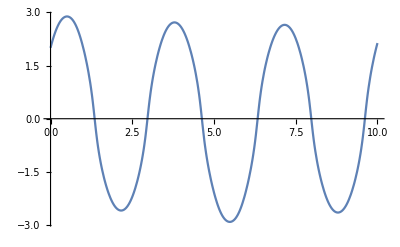

```mathematica
Plot[Evaluate[th1[t]/.sol5], {t, 0,10.0}, PlotRange->All]
```

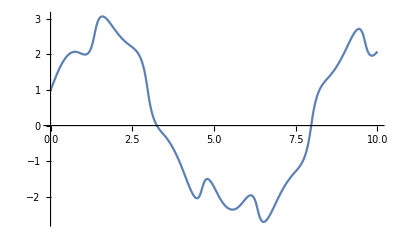

```mathematica
Plot[Evaluate[x[t]/.sol5], {t,0,10.0}, PlotRange->All]
```

```mathematica
deltat1 = 0.1
```

0.1

```mathematica
times2 = Range[0,10, deltat1];

expa11 = Flatten[D[D[(th1[t]/.sol5), t], t]/.t->times2];
expa12 = Flatten[D[D[(x[t]/.sol5), t], t]/.t->times2];
results2 = Transpose[{expth11, expth12, expw11, expw12, expa11, expa12}];
Export["spring_pendulum.csv", resuexpw11 = Flatten[D[(th1[t]/.sol5), t]/.t->times2];lts2, "CSV"];
```

Transpose::nmtx: The first two levels of («1») cannot be transposed.

```mathematica
expth11 = Flatten[(th1[t]/.sol5)/.t->times2];
```

```mathematica
expth12 = Flatten[(x[t]/.sol5)/.t->times2];
```

```mathematica
expw11 = Flatten[D[(th1[t]/.sol5), t]/.t->times2];
```